```mathematica
Exit[]
```

```mathematica
c[u_,v_,a_,b_]:= (1+((u^(-a)-1)^b+(v^(-a)-1)^b)^(1/b))^(-1/a)
```

```mathematica
dA=Simplify[D[c[u1,x,a1,1],x]/.x->t]
```

t^(-1-a1) (-1+t^-a1+u1^-a1)^(-(1+a1)/a1)

```mathematica
dB=D[c[x,u3,a2,1],x]/.x->t
```

t^(-1-a2) (-1+t^-a2+u3^-a2)^(-1-1/a2)

```mathematica
Co=Simplify[c[dA,dB,a3,1]]
```

1/(√(-1+(11.5893+1/t^1.1)^3.81818 t^4.2+(0.371742+1/t^3)^(8/3) t^8))

```mathematica
NIntegrate[Co,{t,0,1}]
```

0.0999968

```mathematica
a1=1.1;a2=3;u1=0.1;u3=0.9
```

0.9

```mathematica
u2=.
```

```mathematica
a3=2;
```

```mathematica
g=;
```

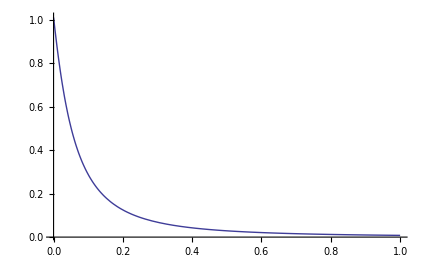

```mathematica
g=Normal[Series[Co,{t,1,150}]];Plot[g,{t,0,1},PlotRange->All]
```

```mathematica
g
```

0.00794295-0.0153552 (-1+t)+0.0218487 (-1+t)^2-0.0273498 (-1+t)^3+0.0318784 (-1+t)^4-0.0354939 (-1+t)^5+0.0382729 (-1+t)^6-0.0402987 (-1+t)^7+0.0416558 (-1+t)^8-0.0424264 (-1+t)^9+0.0426885 (-1+t)^10-0.042515 (-1+t)^11+0.0419728 (-1+t)^12-0.041123 (-1+t)^13+0.0400209 (-1+t)^14-0.0387157 (-1+t)^15+0.0372513 (-1+t)^16-0.0356663 (-1+t)^17+0.0339947 (-1+t)^18-0.0322658 (-1+t)^19+0.0305051 (-1+t)^20-0.028734 (-1+t)^21+0.026971 (-1+t)^22-0.0252315 (-1+t)^23+0.0235279 (-1+t)^24-0.0218707 (-1+t)^25+0.020268 (-1+t)^26-0.0187262 (-1+t)^27+0.01725 (-1+t)^28-0.0158428 (-1+t)^29+0.0145066 (-1+t)^30-0.0132428 (-1+t)^31+0.0120514 (-1+t)^32-0.0109321 (-1+t)^33+0.00988378 (-1+t)^34-0.00890484 (-1+t)^35+0.00799333 (-1+t)^36-0.00714696 (-1+t)^37+0.0063632 (-1+t)^38-0.00563935 (-1+t)^39+0.00497257 (-1+t)^40-0.00435995 (-1+t)^41+0.00379856 (-1+t)^42-0.00328545 (-1+t)^43+0.0028177 (-1+t)^44-0.00239246 (-1+t)^45+0.00200691 (-1+t)^46-0.00165835 (-1+t)^47+0.00134415 (-1+t)^48-0.00106181 (-1+t)^49+0.000808914 (-1+t)^50-0.000583185 (-1+t)^51+0.000382451 (-1+t)^52-0.000204661 (-1+t)^53+0.0000478864 (-1+t)^54+0.0000896884 (-1+t)^55-0.000209762 (-1+t)^56+0.000313921 (-1+t)^57-0.000403643 (-1+t)^58+0.000480304 (-1+t)^59-0.000545176 (-1+t)^60+0.000599438 (-1+t)^61-0.000644178 (-1+t)^62+0.000680397 (-1+t)^63-0.000709014 (-1+t)^64+0.000730874 (-1+t)^65-0.000746747 (-1+t)^66+0.00075734 (-1+t)^67-0.000763292 (-1+t)^68+0.000765187 (-1+t)^69-0.000763553 (-1+t)^70+0.00075887 (-1+t)^71-0.000751568 (-1+t)^72+0.000742036 (-1+t)^73-0.000730623 (-1+t)^74+0.00071764 (-1+t)^75-0.000703369 (-1+t)^76+0.000688055 (-1+t)^77-0.000671921 (-1+t)^78+0.000655161 (-1+t)^79-0.000637946 (-1+t)^80

```mathematica
gg=g/.t->(t+1);
```

```mathematica
NIntegrate[gg,{t,-1,0}]
```

0.100033

```mathematica
NIntegrate[Co,{t,0,1}]
```

0.0999968

```mathematica
NIntegrate[g,{t,0,1}]
```

0.100015

```mathematica
Integrate[(t-x)^n,{t,0,1}]
```

```mathematica
((1-x)^(1+n)+(-x)^n x)/(1+n)/.x->0.2/.n->11
```

0.00572662

```mathematica
$Assumptions=1>x>0&&n>0
```

1>x>0&&n>0

```mathematica
((1-x)^(n+1)+(-x)^(n+1))/(n+1)/.x->0.2/.n->11
```

0.00572662

```mathematica
ab={Co,D[Co,{t,1}],D[Co,{t,2}],D[Co,{t,3}],D[Co,{t,4}],D[Co,{t,5}],D[Co,{t,6}],D[Co,{t,7}],D[Co,{t,8}],D[Co,{t,9}],D[Co,{t,10}],D[Co,{t,11}],D[Co,{t,12}]}/.t->T;
```

```mathematica
ab/Table[n!,{n,0,12}]/.T->0.1
```

{0.287667,-2.89569,20.7606,-126.03,676.746,-3202.18,12524.7,-29125.3,-124737.,2.66501×10^6,-2.8417×10^7,2.54132×10^8,-2.1183×10^9}

```mathematica
D[Co,{t,20}]/20!/.t->1
```

0.0304978